```mathematica
Data = Import["C:\\Users\\jkunimune\\Dropbox\\Work\\EAE\\Hourly_Data\\clean_wind_data.csv"];
```

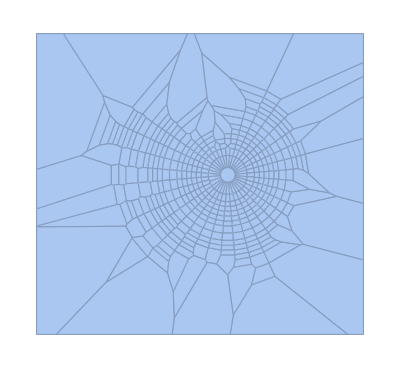

```mathematica
pts = Take[Data,{1,Length[Data]},{1,2}];
vor=VoronoiMesh[pts]
```

```mathematica
ListPointPlot3D[Data[[All,{1,2,3}]], Filling->Bottom, ImageSize->Medium,ColorFunction->"DarkRainbow",AxesLabel->{"X","Y","Concentration"},PlotStyle->PointSize[.018],PlotLabel->Style["Concentration of CO vs. Wind Velocity",FontSize->14]]
```

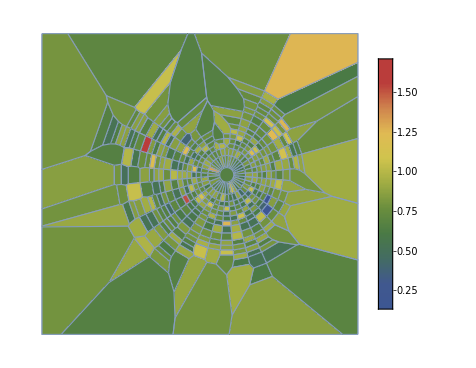

```mathematica
col = Data[[All,3]];
{minQual,maxQual}={Min[#],Max[#]}&@col;
Legended[HighlightMesh[vor,Style@@@({{2,#},ColorData["DarkRainbow"][Rescale[col[[#]],{minQual,maxQual}]]}&/@Range[MeshCellCount[vor,2]])],BarLegend[{"DarkRainbow",{minQual,maxQual}}]]
```

```mathematica
ListPointPlot3D[Data[[All,{1,2,4}]], Filling->Bottom, ImageSize->Medium,ColorFunction->"DarkRainbow",AxesLabel->{"X","Y","Concentration"},PlotStyle->PointSize[.018],PlotLabel->Style["Concentration of NO2 vs. Wind Velocity",FontSize->14]]
```

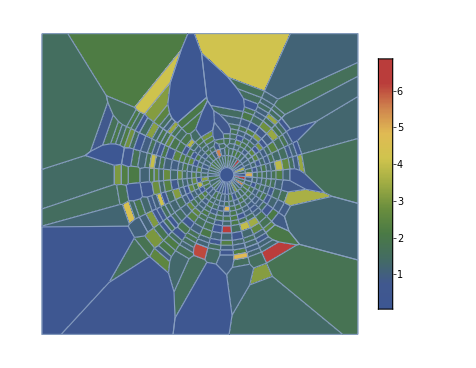

```mathematica
col = Data[[All,4]];
{minQual,maxQual}={Min[#],Max[#]}&@col;
Legended[HighlightMesh[vor,Style@@@({{2,#},ColorData["DarkRainbow"][Rescale[col[[#]],{minQual,maxQual}]]}&/@Range[MeshCellCount[vor,2]])],BarLegend[{"DarkRainbow",{minQual,maxQual}}]]
```

```mathematica
ListPointPlot3D[Data[[All,{1,2,5}]], Filling->Bottom, ImageSize->Medium,ColorFunction->"DarkRainbow",AxesLabel->{"X","Y","Concentration"},PlotStyle->PointSize[.018],PlotLabel->Style["Concentration of O3 vs. Wind Velocity",FontSize->14]]
```

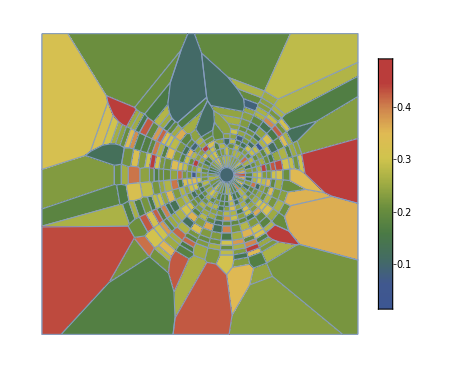

```mathematica
col = Data[[All,5]];
{minQual,maxQual}={Min[#],Max[#]}&@col;
Legended[HighlightMesh[vor,Style@@@({{2,#},ColorData["DarkRainbow"][Rescale[col[[#]],{minQual,maxQual}]]}&/@Range[MeshCellCount[vor,2]])],BarLegend[{"DarkRainbow",{minQual,maxQual}}]]
```

```mathematica
ListPointPlot3D[Data[[All,{1,2,6}]], Filling->Bottom, ImageSize->Medium,ColorFunction->"DarkRainbow",AxesLabel->{"X","Y","Concentration"},PlotStyle->PointSize[.018],PlotLabel->Style["Concentration of SO2 vs. Wind Velocity",FontSize->14]]
```

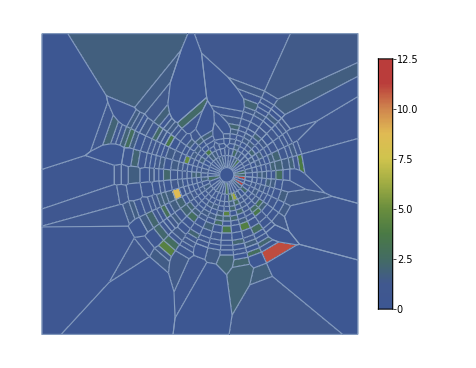

```mathematica
col = Data[[All,6]];
{minQual,maxQual}={Min[#],Max[#]}&@col;
Legended[HighlightMesh[vor,Style@@@({{2,#},ColorData["DarkRainbow"][Rescale[col[[#]],{minQual,maxQual}]]}&/@Range[MeshCellCount[vor,2]])],BarLegend[{"DarkRainbow",{minQual,maxQual}}]]
```

```mathematica
ListPointPlot3D[Data[[All,{1,2,7}]], Filling->Bottom, ImageSize->Medium,ColorFunction->"DarkRainbow",AxesLabel->{"X","Y","Concentration"},PlotStyle->PointSize[.018],PlotLabel->Style["Concentration of PM2.5 vs. Wind Velocity",FontSize->14]]
```

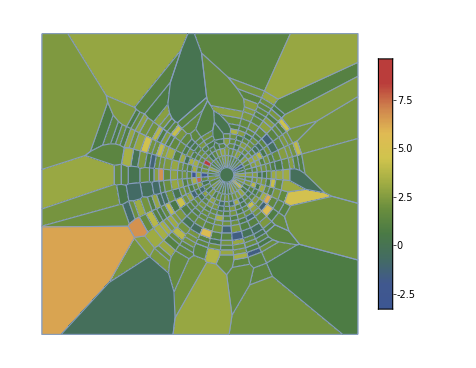

```mathematica
col = Data[[All,7]];
{minQual,maxQual}={Min[#],Max[#]}&@col;
Legended[HighlightMesh[vor,Style@@@({{2,#},ColorData["DarkRainbow"][Rescale[col[[#]],{minQual,maxQual}]]}&/@Range[MeshCellCount[vor,2]])],BarLegend[{"DarkRainbow",{minQual,maxQual}}]]
```

```mathematica
ListPointPlot3D[Data[[All,{1,2,8}]], Filling->Bottom, ImageSize->Medium,ColorFunction->"DarkRainbow",AxesLabel->{"X","Y","Concentration"},PlotStyle->PointSize[.018],PlotLabel->Style["Concentration of PM10 vs. Wind Velocity",FontSize->14]]
```

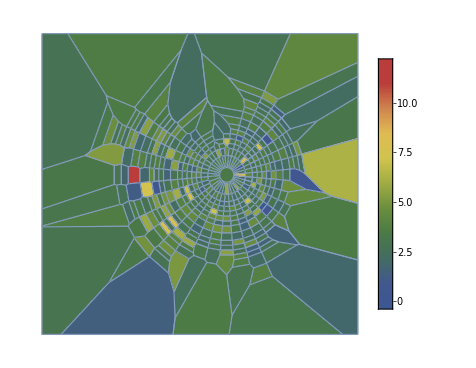

```mathematica
col = Data[[All,8]];
{minQual,maxQual}={Min[#],Max[#]}&@col;
Legended[HighlightMesh[vor,Style@@@({{2,#},ColorData["DarkRainbow"][Rescale[col[[#]],{minQual,maxQual}]]}&/@Range[MeshCellCount[vor,2]])],BarLegend[{"DarkRainbow",{minQual,maxQual}}]]
```